# Quantum Teleportation

## Implementation quantum teleportation using the Q3 Application

## Example 1. Input State is Chosen Randomly

```mathematica
Quit[]
```

```mathematica
<<Q3`Quisso`
```

Q3/Quisso.m v1.9 (2020-11-07) Mahn-Soo Choi

```mathematica
Let[Qubit,S]
```

Bob chooses randomly the state to teleport to Alice, and prepare the third Qubit S[3,None] in it.

```mathematica
in=Basis[S[3]].Normalize@RandomReal[{-1,1},2]
```

-0.537006 ␣+0.843578 1_S_3

Check the normalization of the state.

```mathematica
Dagger[in]**in//Chop
```

1.

Here is the quantum circuit of teleportation.

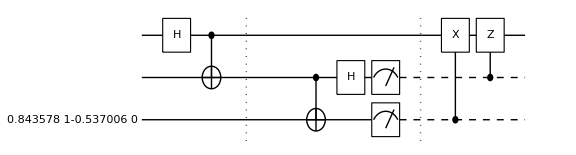

```mathematica
qc=QuissoCircuit[
in,LogicalForm[Ket[],S@{1,2}],
S[1,6],CNOT[S[1],S[2]],"Separator","Spacer",
CNOT[S[2],S[3]],
S[2,6],{Measure[S[2]],Measure[S[3]]},"Separator",
ControlledU[S[3],S[1,1]],
ControlledU[S[2],S[1,3]]
]
```

Convert the quantum circuit (represented by QuissoCircuit) to Quisso expression by means of either QuissoExpresssion or Matrix (usually faster).

```mathematica
outAll=QuissoExpression[qc]//Simplify
```

0.843578 1_S_11_S_2-0.537006 1_S_2

Let us examine the state in Alice’s qubit (S[1,None]).

```mathematica
out=Last@QuissoFactor[outAll,S[{2,3}]]//Simplify;
out//LogicalForm
```

-0.537006 0_S_1+0.843578 1_S_1

You can see the state is the same as the input state. In case, there is irrelevant overall phase factor, let us check the fidelity.

```mathematica
Fidelity[Matrix@in,Matrix@out]
```

1.

As the quantum teleportation is deterministic, Bob’s Bell measurement result does not matter. For the heuristic purposes, let us take a look at Bob’s measurement statistics.

```mathematica
val=Table[
out=QuissoExpression[qc]//Simplify;
Readout[S[{2,3}],out],
{50}
];
Histogram3D[val]
```

-Graphics3D-

## Example 2. Input State is Prepared by Rotations

```mathematica
Quit[]
```

```mathematica
<<Q3`Quisso`
```

Q3/Cauchy.m v1.10 (2020-11-02) Mahn-Soo Choi

Q3/Pauli.m v1.3 (2020-11-02) Mahn-Soo Choi

Q3/Quisso.m v1.2 (2020-11-02) Mahn-Soo Choi

```mathematica
Let[Qubit,S]
```

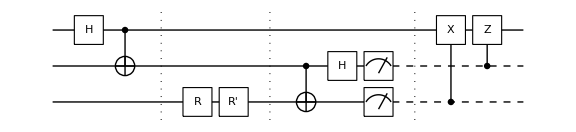

```mathematica
Rz=Rotation[S[3,3],Pi/3,Label->"R"];
Ry=Rotation[S[3,2],Pi/6,Label->Superscript["R",′]];
qc=QuissoCircuit[
Ket[],
S[1,6],CNOT[S[1],S[2]],"Separator",
Rz,Ry,"Separator",
CNOT[S[2],S[3]],
S[2,6],{Measure[S[2]],Measure[S[3]]},"Separator",
ControlledU[S[3],S[1,1]],
ControlledU[S[2],S[1,3]]
];
gr=Graphics[qc,ImageSize->Large]
```

Converting the QuissoCircuit to Quisso expression,

```mathematica
out=QuissoExpression[qc]//Simplify
w=QuissoFactor[out,S[{2,3}]]//Simplify;
w//LogicalForm
v=Rz**Ry**Ket[]//Simplify;
LogicalForm[v]
```

((-1-ⅈ) ((-2+ⅈ)+√3) 1_S_11_S_2+(1-ⅈ) ((2+ⅈ)+√3) 1_S_2)/(4 √2)

1_S_20_S_3⊗(((1-ⅈ) ((2+ⅈ)+√3) 0_S_1-(1+ⅈ) ((-2+ⅈ)+√3) 1_S_1)/(4 √2))

((1/4-ⅈ/4) (((2+ⅈ)+√3) 0_S_3+((2+ⅈ)-√3) 1_S_3))/(√2)

```mathematica
val=Table[
out=QuissoExpression[qc]//Simplify;
Readout[S[{2,3}],out],
{50}
];
Histogram3D[val]
```

-Graphics3D-

Explicitly constructing the Quisso expression,

```mathematica
vec=Multiply[
ControlledU[S[2],S[1,3]],
ControlledU[S[3],S[1,1]],
Measure[S[2]][Measure[S[3]][
Simplify@Multiply[S[2,6],
CNOT[S[2],S[3]],
Rz,Ry,
CNOT[S[1],S[2]],
S[1,6],
Ket[S[{1,2,3}]->1]]]]]//Simplify;
QuissoFactor[vec,S[{2,3}]]
orig=Rz**Ry**Ket[]//Simplify
```

1_S_20_S_3⊗(((1/4+ⅈ/4) (((-2+ⅈ)-√3) ␣+((-2+ⅈ)+√3) 1_S_1))/(√2))

((1/4-ⅈ/4) (((2+ⅈ)+√3) ␣+((2+ⅈ)-√3) 1_S_3))/(√2)